```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Ben\Dropbox\Bayesian book\Figures

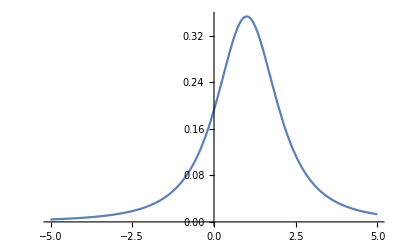

```mathematica
Plot[PDF[StudentTDistribution[1,1,2],x],{x,-5,5}]
```

```mathematica
realData = RandomVariate[StudentTDistribution[1,1,2],{200}];
```

```mathematica
gNormal=Histogram[{realData,normalSimulated},20,ChartStyle->{Blue,Orange},Frame->{True,True,False,False},FrameLabel->{"return %","frequency"},BaseStyle->{FontSize->14},PlotRange->{{-20,20},Full},Axes->{True,False},PlotLabel->"normal",ChartLegends->Placed[{"actual","simulated"},{0.5,0.5}]]
```

-Graphics-

```mathematica
Mean@realData
```

1.19452

```mathematica
Variance@realData
```

7.32499

```mathematica
normalSimulated = RandomVariate[NormalDistribution[1.2,Sqrt@8.3],{200}];
```

```mathematica
tSimulated = RandomVariate[StudentTDistribution[1,1,2],{200}];
```

```mathematica
gT=Histogram[{realData,tSimulated},20,ChartStyle->{Blue,Orange},Frame->{True,True,False,False},FrameLabel->{"return %","frequency"},BaseStyle->{FontSize->14},PlotRange->{{-20,20},Full},Axes->{True,False},PlotLabel->"t-distribution",ChartLegends->Placed[{"actual","simulated"},{0.5,0.5}]]
```

-Graphics-

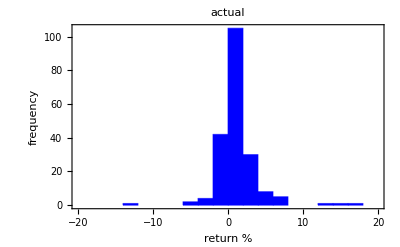

```mathematica
gData = Histogram[realData,20,ChartStyle->Blue,Frame->{True,True,False,False},FrameLabel->{"return %","frequency"},BaseStyle->{FontSize->14},PlotRange->{{-20,20},Full},Axes->{True,False},PlotLabel->"actual"]
```

```mathematica
gFinal=Show[GraphicsRow[{gData,gNormal,gT}],ImageSize->1200]
```

-Graphics-

```mathematica
Export["Posterior_PPCstockReturns.pdf",gFinal]
```

Posterior_PPCstockReturns.pdf